Supplementary Material for 
Dynamical Behavior of the SEIARM - COVID - 19 related Models
by Navid Amiri Babaei, Martin Kröger, and Teoman Özer
June 2024

## Setting up and Solving the SEIARM equations

```mathematica
SolveNumerically:=Module[{},
	ODE[1]=S'[t]==-etap (II[t]+Psi A[t])S[t]/n-mu S[t]+pip -etaw S[t]M[t];
	ODE[2]=EE'[t]==etap (II[t]+Psi A[t])S[t]/n-theta rho EE[t]-omega (1-theta) EE[t]-mu EE[t]+etaw S[t]M[t];
	ODE[3]=II'[t]==omega(1-theta) EE[t]-(mu+taup) II[t];
	ODE[4]=A[t]==theta rho EE[t]-(tauap+mu) A[t];
	ODE[5]=R'[t]==tauap A[t]+taup II[t]-mu R[t];
	ODE[6]=M'[t]==Q II[t]+baromega A[t]-PI M[t];
	solution=NDSolve[{ODE[1],ODE[2],ODE[3],ODE[4],ODE[5],ODE[6],S[0]==S0,EE[0]==E0,II[0]==I0,A[0]==A0,R[0]==R0,M[0]==M0},{S[t],EE[t],II[t],A[t],R[t],M[t]},{t,0,tmax}];
	myS[t_]=S[t]/.solution; 
	myE[t_]=EE[t]/.solution; 
	myI[t_]=II[t]/.solution; 
	myA[t_]=A[t]/.solution; 
	myR[t_]=R[t]/.solution; 
	myM[t_]=M[t]/.solution; 
	p1[t_]=myS[t];
	q1[t_]=myE[t];
	p2[t_]=myI[t];
	q2[t_]=myA[t];
	p3[t_]=myR[t];
	q3[t_]=myM[t];
	Print["Available: p1[t], q2[t], etc. as well as myS[t], myE[t] etc. for times t up to t=",tmax];
];

SolveAnalytically:=Module[{},
	dSdt[t_]:=-etap (II[t]+Psi A[t])S[t]/n-mu S[t]+pip -etaw S[t]M[t];
	dEdt[t_]:=etap (II[t]+Psi A[t])S[t]/n-theta rho EE[t]-omega (1-theta) EE[t]-mu EE[t]+etaw S[t]M[t];
	dIdt[t_]:=omega(1-theta) EE[t]-(mu+taup) II[t];
	dAdt[t_]:=theta rho EE[t]-(tauap+mu) A[t];
	dRdt[t_]:=tauap A[t]+taup II[t]-mu R[t];
	dMdt[t_]:=Q II[t]+baromega A[t]-PI M[t];
	ODE[1]=S'[t]==dSdt[t];
	ODE[2]=EE'[t]==dEdt[t];
	ODE[3]=II'[t]==dIdt[t];
	ODE[4]=A[t]==dAdt[t];
	ODE[5]=R'[t]==dRdt[t];
	ODE[6]=M'[t]==dMdt[t];
	solution=DSolve[{ODE[1],ODE[2],ODE[3],ODE[4],ODE[5],ODE[6],S[0]==S0,EE[0]==E0,II[0]==I0,A[0]==A0,R[0]==R0,M[0]==M0},{S[t],EE[t],II[t],A[t],R[t],M[t]},t];
	myS[t_]=S[t]/.solution; 
	myE[t_]=EE[t]/.solution; 
	myI[t_]=II[t]/.solution; 
	myA[t_]=A[t]/.solution; 
	myR[t_]=R[t]/.solution; 
	myM[t_]=M[t]/.solution; 
	p1[t_]=myS[t];
	q1[t_]=myE[t];
	p2[t_]=myI[t];
	q2[t_]=myA[t];
	p3[t_]=myR[t];
	q3[t_]=myM[t];
	Print["Available: p1[t], q2[t], etc. as well as myS[t], myE[t] etc. for arbitrary times t"];
];

SHOW[quantity_]:=Plot[quantity[t],{t,0,tmax},
	Frame->True,FrameLabel->{t,Style[quantity,FontFamily->"Arial",FontSize->20]},
	FrameStyle->{FontFamily->"Helvetica",FontSize->20}
];
```

## Default parameters and initial values

```mathematica
ClearParameters:=Module[{},
	Clear[etaw,etap,mu,theta,pip,taup,tauap,rho,baromega,PI,omega,Q,Psi,n];
	pip=mu n;
]
```

```mathematica
ClearInitialConditions:=Module[{},
	Clear[S0,E0,I0,A0,R0,M0];
	n=S0+E0+I0+A0+R0;
];
```

```mathematica
DefaultParameters:=Module[{},
etaw=1.231/10^6;
etap=0.05;
mu=0.005;
theta=0.413;
pip=mu n;
taup=0.09871;
tauap=0.3912;
rho=0.005;
baromega=0.0001;
PI=0.01;
omega=4.7876/10^3;
Q=2.98/10^4;
Psi=1;
n=8266000];
```

```mathematica
DefaultInitialConditions:=Module[{},
S0=8065518; 
E0=200000;
I0=282;
A0=200;
R0=0;
M0=50000];
```

## Defining special cases

```mathematica
Table3Case1NoInfection:=Module[{},
	tauap=taup;
	PI=mu;
	Psi=0
];
```

```mathematica
Table3Case1CertainInfection:=Module[{},
	tauap=taup;
	PI=mu;
	Psi=1
];
```

```mathematica
Table5Case23PartialInfection:=Module[{},
	theta=0;
	tauap=omega;
	Psi=pip etaw(taup baromega-Q omega)/(etap mu taup(mu+omega-PI))+omega/taup;
];
```

## Solution to the unconstrained SEIARM equations

```mathematica
DefaultParameters;
DefaultInitialConditions;
SolveNumerically
```

NDSolve::ivres: NDSolve has computed initial values that give a zero residual for the differential-algebraic system, but some components are different from those specified. If you need them to be satisfied, giving initial conditions for all dependent variables and their derivatives is recommended.

Available: p1[t], q2[t], etc. as well as myS[t], myE[t] etc. for times t up to t=500

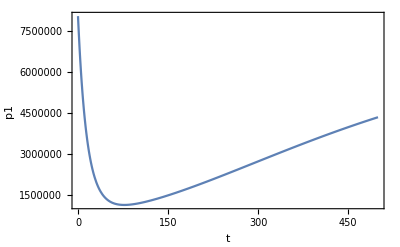

```mathematica
SHOW[p1]
```

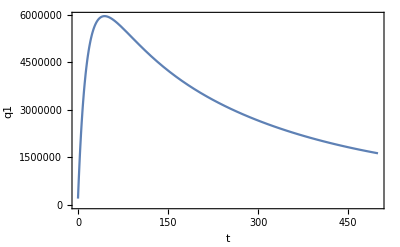

```mathematica
SHOW[q1]
```

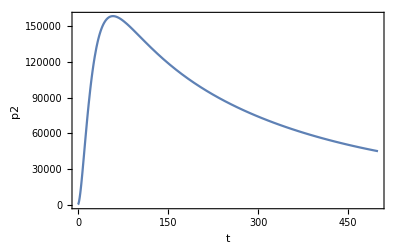

```mathematica
SHOW[p2]
```

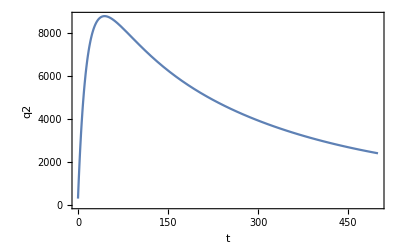

```mathematica
SHOW[q2]
```

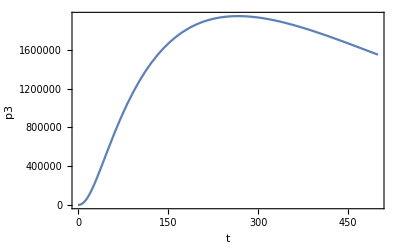

```mathematica
SHOW[p3]
```

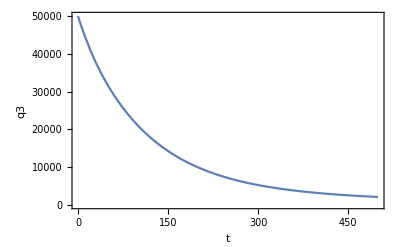

```mathematica
SHOW[q3]
```

## Special solution (Table 3, Case 1, No infection) to the SEIARM equations

```mathematica
DefaultParameters;
DefaultInitialConditions;
Table3Case1NoInfection;
SolveNumerically
```

NDSolve::ivres: NDSolve has computed initial values that give a zero residual for the differential-algebraic system, but some components are different from those specified. If you need them to be satisfied, giving initial conditions for all dependent variables and their derivatives is recommended.

Available: p1[t], q2[t], etc. as well as myS[t], myE[t] etc. for times t up to t=500

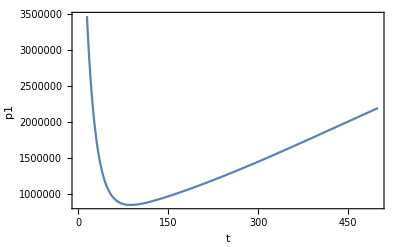

```mathematica
SHOW[p1]
```

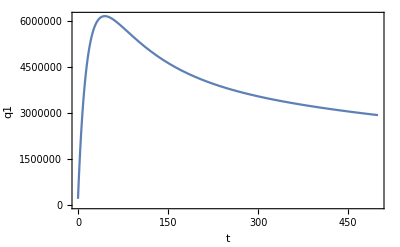

```mathematica
SHOW[q1]
```

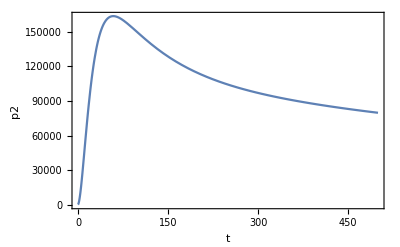

```mathematica
SHOW[p2]
```

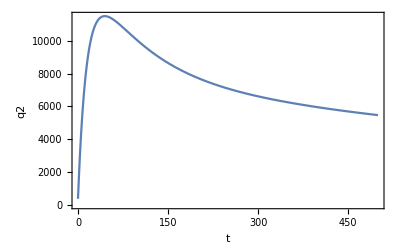

```mathematica
SHOW[q2]
```

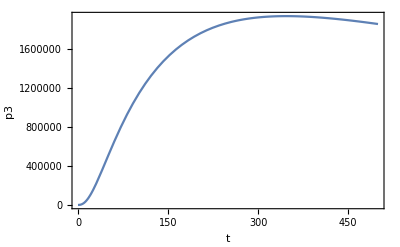

```mathematica
SHOW[p3]
```

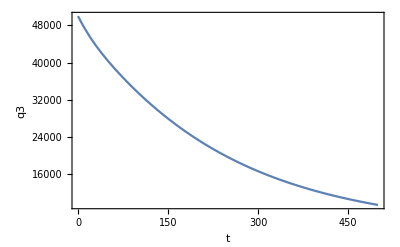

```mathematica
SHOW[q3]
```

## Special solution (Table 3, Case 1, Certain infection) to the SEIARM equations

```mathematica
DefaultParameters;
DefaultInitialConditions;
Table3Case1CertainInfection;
tmax=500;
SolveNumerically
```

NDSolve::ivres: NDSolve has computed initial values that give a zero residual for the differential-algebraic system, but some components are different from those specified. If you need them to be satisfied, giving initial conditions for all dependent variables and their derivatives is recommended.

Available: p1[t], q2[t], etc. as well as myS[t], myE[t] etc. for times t up to t=500

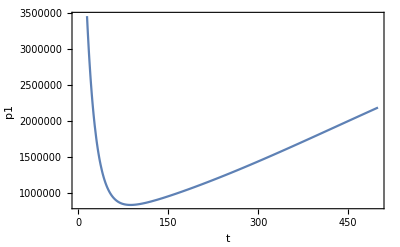

```mathematica
SHOW[p1]
```

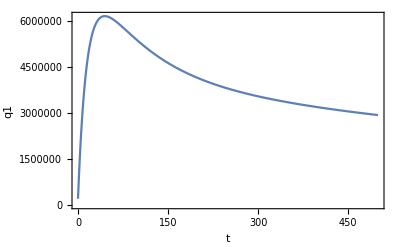

```mathematica
SHOW[q1]
```

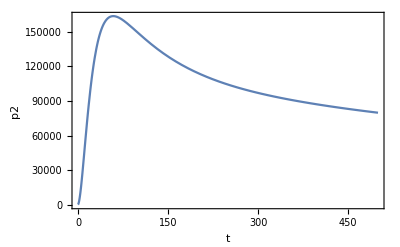

```mathematica
SHOW[p2]
```

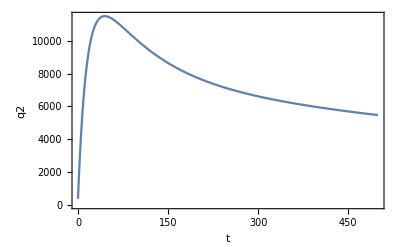

```mathematica
SHOW[q2]
```

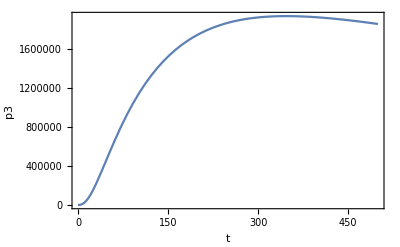

```mathematica
SHOW[p3]
```

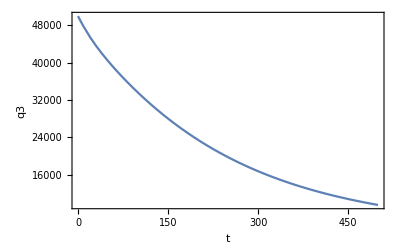

```mathematica
SHOW[q3]
```